```mathematica
(*Inputs*)
g=1.5;
κ=0.2;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"];
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])];data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x] +g^2;
```

InterpolatingFunction::dmval: Input value {1.66752×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.66939×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.67127×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

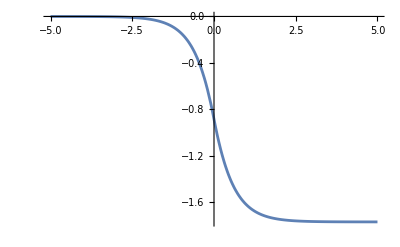

```mathematica
Plot[ϕss[x],{x,-5,5}]
```

1.67785

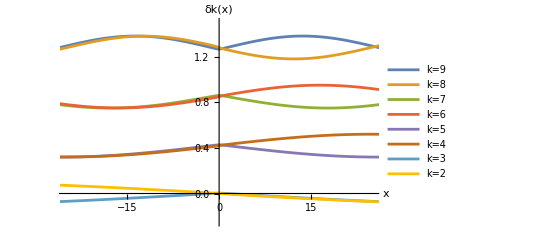

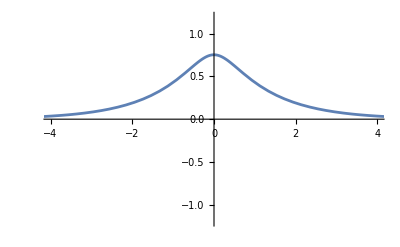

```mathematica
L=200;
dx=.01;
total=100;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
(*total=800;
vals=Import["/scratch/network/zz3250/valsL300dxp01g1p5_total800.wl"];
fns=Import["/scratch/network/zz3250/vecsL300dxp01g1p5_total800.wl"];*)
Print[Sqrt[vals[[1]]]]
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[-fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-150,150},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[-fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

```mathematica
(*dealing with mathematica being weird*)
xRange=Range[-100,100,dx];
originalData=Table[{x,-fns[[1]]/.x->x},{x,xRange}];
ϕb=Interpolation[originalData];
```

```mathematica
ϕb[0]
λ1=1;
ωb=Sqrt[vals[[1]]];
λ4=4*Pi^2/3;
Γ=3*λ4/(8*ωb^2)*NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-150,150}];
```

0.752301

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0654829 and 1.12028×10^-6 for the integral and error estimates.

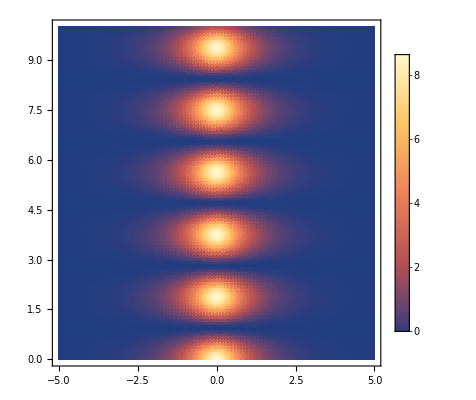

```mathematica
(*Expecatation value of meson field in a number state*)
(*n=0*)
nb=0;
expNbMesonField[x_,t_]:=-(λ1*ϕb[0]/(Γ*ωb*(2*nb+1)))*ϕb[x]*Cos[ωb*t]
DensityPlot[Abs[expNbMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

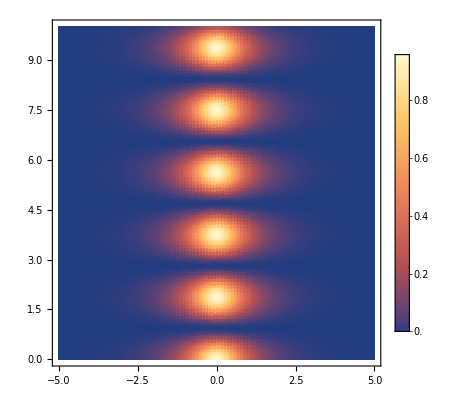

```mathematica
(*n=1*)
nb=1;
expNbMesonField[x_,t_]:=-(λ1*ϕb[0]/(Γ*ωb*(2*nb+1)))*ϕb[x]*Cos[ωb*t]
DensityPlot[Abs[expNbMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

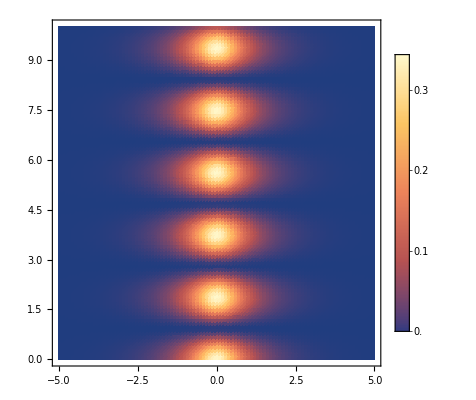

```mathematica
(*n=2*)
nb=2;
expNbMesonField[x_,t_]:=-(λ1*ϕb[0]/(Γ*ωb*(2*nb+1)))*ϕb[x]*Cos[ωb*t]
DensityPlot[Abs[expNbMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

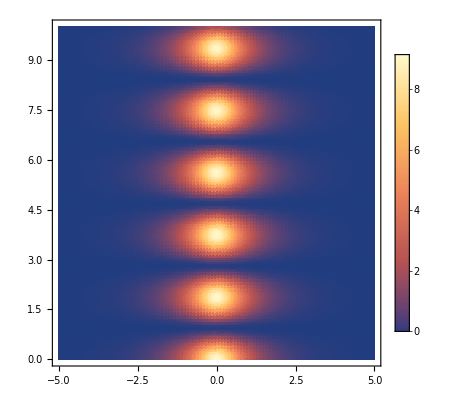

```mathematica
(*Coherent bound state*)
(*α=.5*)
α=.25;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

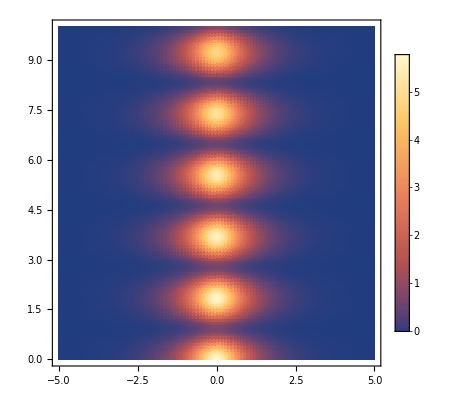

```mathematica
(*α=1*)
α=1;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

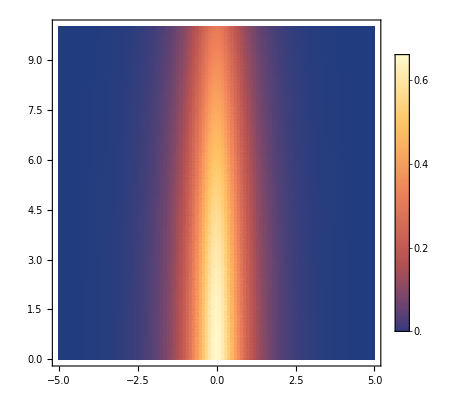

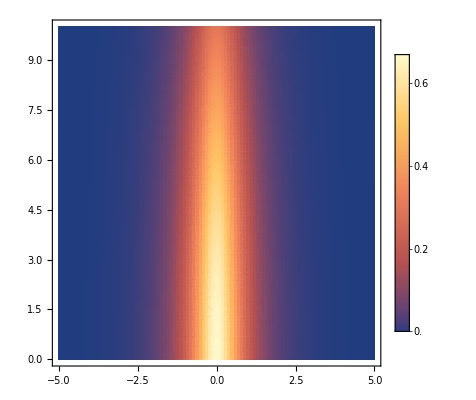

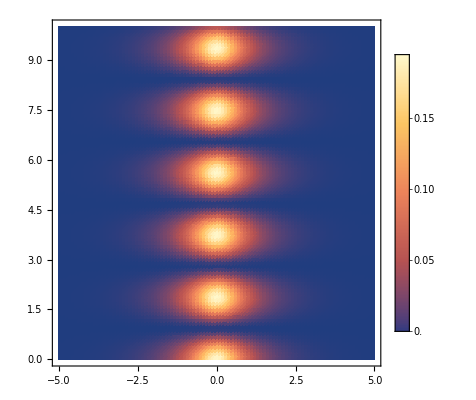

```mathematica
(*more details on alpha 1 scenario*)
α=2;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
DensityPlot[Abs[coeff*ϕb[x]*firstterm[t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
DensityPlot[Abs[coeff*ϕb[x]*secondterm[t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
DensityPlot[Abs[ϕb[x]*thirdterm[t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

```mathematica
(*α=2*)
α=2;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->3,PlotPoints->200,PlotRange->All]
```

-Graphics-

```mathematica
(*α=3*)
α=3;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->3,PlotPoints->200,PlotRange->All]
```

-Graphics-

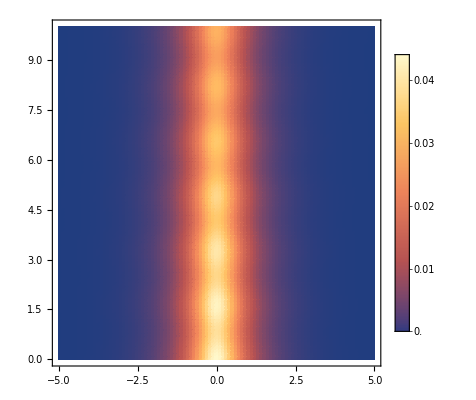

```mathematica
(*α=4*)
α=4;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->2,PlotPoints->100,PlotRange->All]
```

```mathematica
(*α=5*)
α=5;
coeff=Exp[-α^2]/Sqrt[2*ωb];
firstterm[t_]:=(1/α)*Sum[(α^(2*n)/((n-1)!))*Exp[-I*(ωb-2*κ*Γ*n)*t],{n,1,10}];
secondterm[t_]:=α*Sum[(α^(2*n)/(n!))*Exp[-I*(ωb-2*κ*Γ*n-2*κ*Γ)*t],{n,0,10}];
thirdterm[t_]:=-(λ1*ϕb[0]/(Γ*ωb))*Cos[ωb*t]*Exp[-α^2]*Sum[(α^(2*n)/(n!))*(1/(2*n+1)),{n,0,10}]
expCoherentMesonField[x_,t_]:=coeff*ϕb[x]*(firstterm[t]+secondterm[t])+thirdterm[t]*ϕb[x];
DensityPlot[Abs[expCoherentMesonField[x,t]]^2,{x,-5,5},{t,0,10},PlotLegends->Automatic,MaxRecursion->3,PlotPoints->200,PlotRange->All]
```

-Graphics-

```mathematica
For[i=2,i<=total,i=i+2,
a=fns[[i]]/.x->-.1;
If[a<0,fns[[i]]=-fns[[i]]];
];
For[i=3,i<=total,i=i+2,
a=fns[[i]]/.x->0;
If[a>0,fns[[i]]=-fns[[i]]]
];
```

```mathematica
efuns={};
For[i=2,i<=100,i++,
ψ=fns[[i]];
xRange=Range[-100,100,dx];
originalData=Table[{x,ψ/.x->x},{x,xRange}];
originalInterp=Interpolation[originalData];
AppendTo[efuns,originalInterp];
];
```

```mathematica
(*vev of k states*)
coeff=I*κ*λ1/L;
kcontributions={};
For[i=1,i<=48,i=i+2,
ωk=Sqrt[vals[[i+1]]];
k=Sqrt[ωk^2-g^2-2*Pi*κ];
(*positive k*)
ϕk[x_]:=(1/Sqrt[2])*(efuns[[i+1]][x]+I*efuns[[i]][x]);
ϕkstar[x_]:=(1/Sqrt[2])*(efuns[[i+1]][x]-I*efuns[[i]][x]);
dϕk[x_]:=D[ϕk[X],X]/.X->x;
xdepk[x_]:=-I*dϕk[x]/ϕk[x];
βk=NIntegrate[xdepk[x]*ϕk[x]*ϕkstar[x],{x,-95,95}];
βkstar=Conjugate[βk];
part[x_,t_]:=coeff*(k/(2*ωk)^2)*(ϕkstar[0]*ϕk[x]*(t+(ωk/βk)*x)*Exp[-I*ωk*t]-ϕk[0]*ϕkstar[x]*(t+(ωk/βkstar)*x)*Exp[I*ωk*t]);
AppendTo[kcontributions,part[x,t]];
(*negative k*)
ϕk[x_]:=(1/Sqrt[2])*(efuns[[i+1]][x]-I*efuns[[i]][x]);
ϕkstar[x_]:=(1/Sqrt[2])*(efuns[[i+1]][x]+I*efuns[[i]][x]);
dϕk[x_]:=D[ϕk[X],X]/.X->x;
xdepk[x_]:=-I*dϕk[x]/ϕk[x];
βk=NIntegrate[xdepk[x]*ϕk[x]*ϕkstar[x],{x,-95,95}];
βkstar=Conjugate[βk];
part[x_,t_]:=coeff*(k/(2*ωk)^2)*(ϕkstar[0]*ϕk[x]*(t+(ωk/βk)*x)*Exp[-I*ωk*t]-ϕk[0]*ϕkstar[x]*(t+(ωk/βkstar)*x)*Exp[I*ωk*t]);
AppendTo[kcontributions,part[x,t]];
];
vevk[x_,t_]=Total[kcontributions];
```

```mathematica
DensityPlot[Abs[vevk[x,t]]^2,{x,-100,100},{t,0,100},PlotLegends->Automatic,MaxRecursion->3,PlotPoints->200,PlotRange->All]
```

-Graphics-

```mathematica
(*1st energy level*)
n=1;
Print["quadratic: ",n*ωb];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-150,150}];
nshift=(κ/2)*(Pi/ωb)^2*Vbbbb;
nsqshift=κ*(Pi/ωb)^2*Vbbbb;
Eshift=n*ωb-n*nshift-n^2*nsqshift;
Print["1st order: ",Eshift];
```

quadratic: 1.67785

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0654829 and 1.12028×10^-6 for the integral and error estimates.

1st order: 1.74672

```mathematica
n=2;
Print["quadratic: ",n*ωb];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-150,150}];
nshift=(κ/2)*(Pi/ωb)^2*Vbbbb;
nsqshift=κ*(Pi/ωb)^2*Vbbbb;
Eshift=n*ωb-n*nshift-n^2*nsqshift;
Print["1st order: ",Eshift];
```

quadratic: 3.35569

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0654829 and 1.12028×10^-6 for the integral and error estimates.

1st order: 3.58527

```mathematica
n=3;
Print["quadratic: ",n*ωb];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-150,150}];
nshift=(κ/2)*(Pi/ωb)^2*Vbbbb;
nsqshift=κ*(Pi/ωb)^2*Vbbbb;
Eshift=n*ωb-n*nshift-n^2*nsqshift;
Print["1st order: ",Eshift];
```

quadratic: 5.03354

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0654829 and 1.12028×10^-6 for the integral and error estimates.

1st order: 5.51564

```mathematica
n=4;
Print["quadratic: ",n*ωb];
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-150,150}];
nshift=(κ/2)*(Pi/ωb)^2*Vbbbb;
nsqshift=κ*(Pi/ωb)^2*Vbbbb;
Eshift=n*ωb-n*nshift-n^2*nsqshift;
Print["1st order: ",Eshift];
```

quadratic: 6.71138

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00466249}. NIntegrate obtained -0.0654829 and 1.12028×10^-6 for the integral and error estimates.

1st order: 7.53785

```mathematica
Plot[{7.53785,6.71138,5.51564,5.03354,3.58527,3.355691,1.74672,1.67785,0,0},{x,0,5},PlotStyle->{Brown,{Brown,Dashed},Red,{Red,Dashed},Green,{Green,Dashed},Blue,{Blue,Dashed},Purple,{Purple,Dashed}},PlotLegends->{"E4",None,"E3",None,"E2",None,"E1",None,"E0",None},PlotLabel->"First order energy shift",AxesLabel->{None,"Energy"}]
```

-Graphics-